```mathematica
(*PSO 20 particles, 100 iterations,5 assets*)
data215 = {0.3961000000000924,0.39610005762475775,0.3961000037182159,0.3961000000329766,0.3961000000000106,0.3961000000792122,0.3961000000050603,0.39610000081044017,0.3960999999999998,0.39610000000005324,0.3960999999999999,0.39610000000040896,0.39610000120907946,0.3961000000241184};

(*PSO 20 particles, 300 iterations,5 assets*)
data235 = {0.3960999999999999,0.39609999999999995,0.39609999999999984,0.39609999999999984,0.3960999999999999,0.3961000000000115,0.39609999999999984,0.3960999999999999,0.39609999999999984,0.39609999999999995,0.39609999999999973,0.39609999999999984,0.3960999999999999,0.39609999999999984,0.3960999999999999,0.39609999999999984};

(*PSO 40 particles, 100 iterations,5 assets*)
data415 = {0.3961000000000139,0.39610000057968475,0.3961000000021974,0.39610000000001916,0.39610000000559836,0.39610000000000317,0.39610000004825263,0.39610000000002565,0.39610000023907305,0.39610000000989404,0.39610000000000745,0.39609999999999995,0.3961000000003067,0.39610000000025863,0.396100000000115,0.3960999999999999};

(*PSO 20 particles, 100 iterations,7 assets*)
data217 = {0.47260000000001146,0.4726000000001279,0.47260000000002095,0.4726000000000021,0.4726002472739108,0.47260000000024094,0.4726000218695227,0.4726000002342501,0.47260000000278374,0.4726000865208052,0.4726000000000137,0.4726000000137893,0.47260000000001623,0.47260000095407373,0.47260000624865295,0.4726000001725963};

(*PSO 20 particles, 300 iterations,7 assets*)
data237 = {0.4725999999999998,0.47260000000009916,0.4725999999999998,0.47259999999999985,0.4725999999999999,0.47259999999999974,0.47259999999999985,0.4725999999999998,0.47259999999999974,0.47259999999999985,0.47259999999999985,0.47259999999999985,0.4725999999999998,0.4726000000000395,0.4726000000000011,0.47259999999999985};

(*PSO 40 particles, 100 iterations,7 assets*)
data417 = {0.47259999999999985,0.47260000008571706,0.47260000000001995,0.4726000000000047,0.47260000000164937,0.47259999999999985,0.4726000000000092,0.4726000000000001,0.47259999999999985,0.4726000000000021,0.47260000000262103,0.4726000000059122,0.4726000000000095,0.4725999999999999,0.47259999999999985,0.47260000001618396};
```

```mathematica
(*PSO 20 particles, 100 iterations*)
data1={0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175};
```

```mathematica
{Mean[data1],Median[data2],Median[data3]}
```

{0.3311,0.3311,0.3311}

```mathematica
(*PSO 20 particles, 500 iterations*)
data2 = {0.33109999999999984,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.3311,0.33109999999999984,0.33109999999999984,0.33109999999999984,0.3311000000000085};
```

```mathematica
StandardDeviation[data1]
```

4.47073×10^-12

```mathematica
StandardDeviation[data2]
```

2.2328×10^-15

```mathematica
StandardDeviation[data1](*StdDev for 20np 100nit*)
```

4.47073×10^-12

```mathematica
StandardDeviation[data2](*StdDev for 20np 500nit*)
```

2.60506×10^-15

```mathematica
(*PSO 40 particles, 100 iterations*)data3 = {0.3311000000024352,0.33110000001074713,0.3311000000000046,0.33110000000082634,0.3311000000002402,0.3311000000001075,0.33110000022497593,0.3311000000000255,0.3310999999999999,0.3310999999999999,0.3311};
```

```mathematica
StandardDeviation[data3](*StdDev for 40np 100nit*)
```

6.74743×10^-11

```mathematica
data4=Flatten[Import["~/Desktop/Uni\ shizz\ 4th\ year/CS4525\ Project/Haskell/ghc-eden-7.6.1/testing2.txt","Data"]]

Sort[{0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175},Less]
```

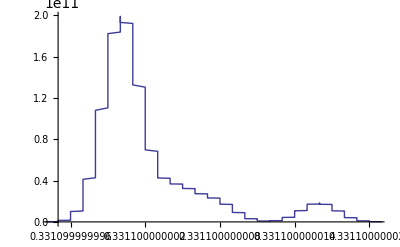

```mathematica
SmoothHistogram[data1,Automatic,"PDF"]
```

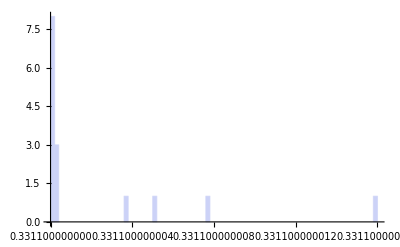

```mathematica
Histogram[data1,100]
```

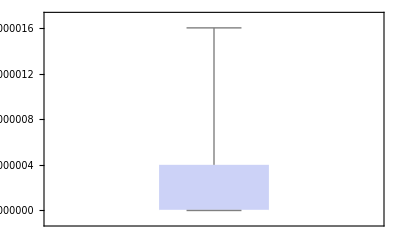

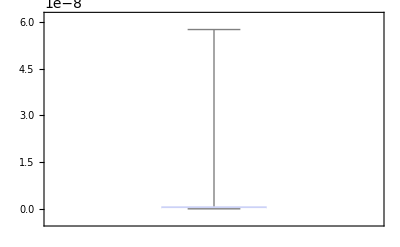

```mathematica
BoxWhiskerChart[{data1}]
BoxWhiskerChart[{dataTest}]
```

```mathematica
dataTest= Function[x,x-0.3961]/@data215
data215
StandardDeviation[dataTest]
StandardDeviation[data215]
```

{9.23706×10^-14,5.76248×10^-8,3.71822×10^-9,3.29766×10^-11,1.06026×10^-14,7.92122×10^-11,5.06029×10^-12,8.1044×10^-10,-2.22045×10^-16,5.32352×10^-14,-1.11022×10^-16,4.08951×10^-13,1.20908×10^-9,2.41184×10^-11}

{0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961,0.3961}

1.53134×10^-8

1.53134×10^-8

```mathematica
dataTest2={data1,data1}
```

{{0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311},{0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311}}

```mathematica
Flatten[%92]
```

{0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311,0.3311}

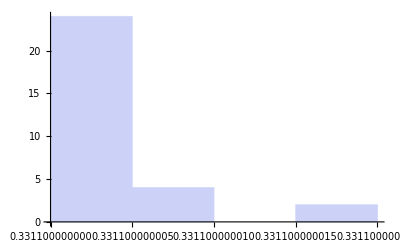

```mathematica
Histogram[%93]
```

```mathematica
StandardDeviation[dataTest2]
```

1.53134×10^-8